```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
$Assumptions={n}∈Integers ∧n>0
```

n∈Integers&&n>0

# Mathematica for Engineering Systems: Part I

## Introduction

The Applied Physics curriculum is being modified, starting from study year 2018, with respect to tools we want students to be professionalized at. We will drop Matlab in favour of Python as a programming and data analysis tool. This change has 
At his point I do not want to go into the details of the motivation, and the choices that have to be made, but only address the possibilities of Mathematica to help you with the job of modelling and simulation.

In this document, an overview is given of the functions that replace the various functions, modules and applications in Matlab. For the replacement of Simulink, we already elaborated on the drop of the graphical programming of this modelling language: after module 5 nobody, no research group and no external company (we know off) uses Simulink. However the need for the simulation of calculation of a non-linear dynamic system remains.

## Continuous-time systems

Differential Equations

Below you will find an method of solving differential equations via state-space systems and transfer functions, generating Bode-Plots, Nyquist Plots, and responses.

#### First-order system

Differential equations can be described in Mathematica and also solved. Let start with a simple first order differential equation:

```mathematica
eqn1=y'[t]+ 1/τ y[t] ==  UnitStep[t]
```

y[t]/τ+y'[t]==UnitStep[t]

The differential equation can also be solved, e.g. with initial condition y[0]=0

```mathematica
dsol1=DSolve[{eqn1,y[0]==0},y[t],t]
```

{{y[t]→ⅇ^(-t/τ) (-1+ⅇ^(t/τ)) τ UnitStep[t]}}

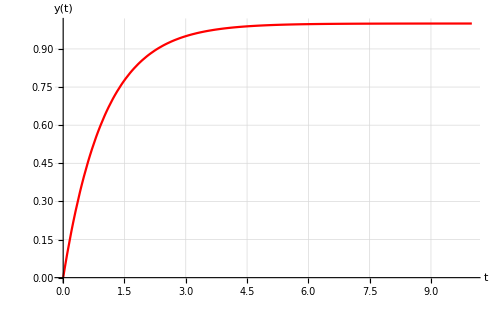

```mathematica
Plot[y[t]/.dsol1/.τ->1,{t,0,10},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

#### Second-order system

Let us now define a second-order system and solve that one with initial conditions and no input.

```mathematica
eqn2=y''[t]+ 2 ζ ω0 y'[t]+ω0^2 y[t]==0
```

ω0^2 y[t]+2 ζ ω0 y'[t]+y''[t]==0

```mathematica
initc={y'[0]== 0,y[0]==2}
```

{y'[0]==0,y[0]==2}

```mathematica
dsol2=DSolve[Flatten[{eqn2,initc}],y[t],t]
```

{{y[t]→1/((-1+ζ^2) ω0)(-ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ω0-ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ω0+ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ζ^2 ω0+ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ζ^2 ω0-ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ζ √((-1+ζ^2) ω0^2)+ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ζ √((-1+ζ^2) ω0^2))}}

```mathematica
y[t]/.dsol2/.{ζ->1/2,ω0->2}
```

{-2/3 (-3/2 ⅇ^((-1-ⅈ √3) t)-1/2 ⅈ √3 ⅇ^((-1-ⅈ √3) t)-3/2 ⅇ^((-1+ⅈ √3) t)+1/2 ⅈ √3 ⅇ^((-1+ⅈ √3) t))}

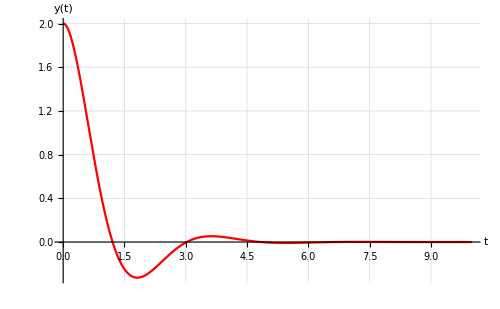

```mathematica
Plot[y[t]/.dsol2/.{ζ->0.5,ω0->2},{t,0,10},PlotRange->Full,GridLines->Automatic,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

#### Solving differential equations is not the core of this course.

Although it is possible to solve differential equations with Mathematica, it is not the core bossiness in this course. The main subject is to get acquainted with various tools and develop a broader insight in the system of modelling. In the previous examples the differential equations were already formulated with the useful parameters: time constant τ for the first order system, and natural frequency ω0 and damping coefficient ζ for the second order system. These parameters can be derived from the plots of the output.

An other way of solving the differential equations is the application of the Laplace transform.

Laplace Transform

### Direct Laplace Transforms and Inverse Laplace Transforms

First we start with a few stand-alone Laplace transforms and inverse transforms. Basically you can check the Laplace pairs in the standard table.

#### a.

```mathematica
LaplaceTransform[Cos[ω t],t,s]
```

s/(s^2+ω^2)

#### b.

```mathematica
InverseLaplaceTransform[ω/(s^2+ω^2),s,t]
```

Sin[t ω]

#### c.

```mathematica
LaplaceTransform[ⅇ^(-γ t)Cos[ω t],t,s]
```

(s+γ)/((s+γ)^2+ω^2)

```mathematica
InverseLaplaceTransform[ⅇ^(-s Subscript[t, 0]),s,t]
```

InverseLaplaceTransform[ⅇ^(-s t_0),s,t]

### Laplace Transform to solve Differential equations

Now we apply Laplace to solve differential equations.

#### a.

```mathematica
lteqn1=LaplaceTransform[y'[t]-3 y[t]==0,t,s]
```

-3 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]-y[0]==0

```mathematica
Solve[lteqn1/.y[0]-> 1,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→1/(-3+s)}}

```mathematica
InverseLaplaceTransform[%,s,t]
```

{{y[t]→ⅇ^(3 t)}}

#### b.

```mathematica
lteqn2=LaplaceTransform[y''[t]+3 y'[t]+2 y[t]==0,t,s]
```

2 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+3 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==0

```mathematica
Solve[lteqn2/.{y'[0]->0,y[0]->2},LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(2 (3+s))/(2+3 s+s^2)}}

```mathematica
InverseLaplaceTransform[%,s,t]
```

{{y[t]→2 ⅇ^(-2 t) (-1+2 ⅇ^t)}}

### Inverse Laplace Transform of a Transfer Function

#### a.

```mathematica
InverseLaplaceTransform[10/(s^3+4 s^2+9 s + 10),s,t]
```

10 (ⅇ^(-2 t)/5-1/20 ⅇ^((-1-2 ⅈ) t) ((2-ⅈ)+(2+ⅈ) ⅇ^(4 ⅈ t)))

```mathematica
%//FullSimplify
```

ⅇ^(-2 t) (2+ⅇ^t (-2 Cos[2 t]+Sin[2 t]))

#### b.

ii

```mathematica
yb2[t_]=InverseLaplaceTransform[1/(s+1)^4,s,t]
```

1/6 ⅇ^-t t^3

iii

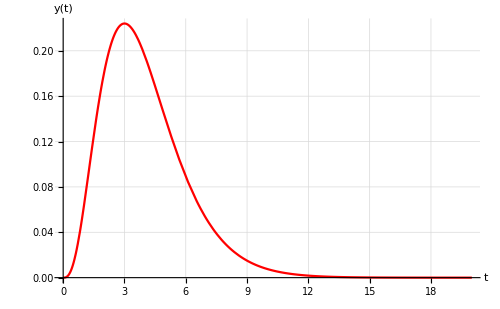

```mathematica
Plot[yb2[t],{t,0,20},GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

```mathematica
yb3[t_]=InverseLaplaceTransform[(s-3)/((s+3)^2+6),s,t]
```

(ⅇ^(-3 t) (√6 Cos[√6 t]-6 Sin[√6 t]))/(√6)

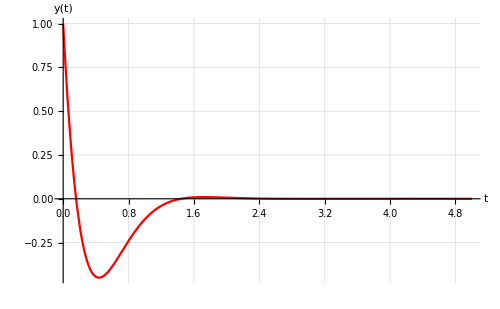

```mathematica
Plot[yb3[t],{t,0,5},PlotRange->All,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

### Inverse Laplace Transform of a step function and a delay

```mathematica
InverseLaplaceTransform[ⅇ^-s/s,s,t]
```

HeavisideTheta[-1+t]

### Partial fraction decomposition

Techniques used with the Laplace transforms can also be used separately.

```mathematica
expr=(s^4+8 s^3+16 s^2+9 s+6)/(s^3+6 s^2+11 s+6)
```

(6+9 s+16 s^2+8 s^3+s^4)/(6+11 s+6 s^2+s^3)

```mathematica
InverseLaplaceTransform[expr,s,t]
```

-6 ⅇ^(-3 t)-4 ⅇ^(-2 t)+3 ⅇ^-t+2 DiracDelta[t]+DiracDelta'[t]

Perform a partial fraction decomposition of the transfer function

```mathematica
exprpf=Apart[expr]
```

2+s+3/(1+s)-4/(2+s)-6/(3+s)

and calculate the inverse Laplace Transform

```mathematica
InverseLaplaceTransform[exprpf,s,t]
```

-6 ⅇ^(-3 t)-4 ⅇ^(-2 t)+3 ⅇ^-t+2 DiracDelta[t]+DiracDelta'[t]

The results are the same, as it should be. Now a direct relation between the terms can be made.

### From Laplace to differential equation

```mathematica
tfToDiff[tf_,s_,t_,y_,u_]:=Module[{rhs,lhs,n,m},rhs=Numerator[tf];
lhs=Denominator[tf];
rhs=rhs/.m_. s^n_.->m D[u[t],{t,n}];
lhs=lhs/.m_. s^n_.->m D[y[t],{t,n}];
lhs==rhs]
tf=(5s)/(s^2+4s+25);
tf=C0 s/(R0 C0 s+1);
eq=tfToDiff[tf,s,t,y,u]
```

1+C0 R0 y'[t]==C0 u'[t]

Transfer functions

With the use of Laplace, a transfer function can be constructed and with this transfer function a transfer function model.

#### First example

```mathematica
sys0=TransferFunctionModel[25/(s^2+4 s+25),s]
```

25/(25+4 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1125251FalseFalseFalseAutomaticNoneAutomatic

And extract the characteristics, like zero’s and poles.

```mathematica
TransferFunctionZeros[sys0]
```

{{{}}}

```mathematica
TransferFunctionPoles[sys0]//N
```

{{{-2.-4.58258 ⅈ,-2.+4.58258 ⅈ}}}

#### Define a general transfer function of second-order:

```mathematica
sys1=TransferFunctionModel[1/(s^2+2 ζ ω0 s + ω0^2),s]
```

1/(ω0^2+2 ζ ω0 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

Define a set of parameters for exploration of the second-order system:

```mathematica
param={{ζ->0.2,ω0->2},{ζ->1/2 √2,ω0->2},{ζ->2,ω0->2}}
```

{{ζ→0.2,ω0→2},{ζ→1/(√2),ω0→2},{ζ→2,ω0→2}}

```mathematica
rsys1=OutputResponse[sys1/.param[[1]],UnitStep[t],t];
```

```mathematica
rsys2=OutputResponse[sys1/.param[[1]],DiracDelta[t-3],t];
```

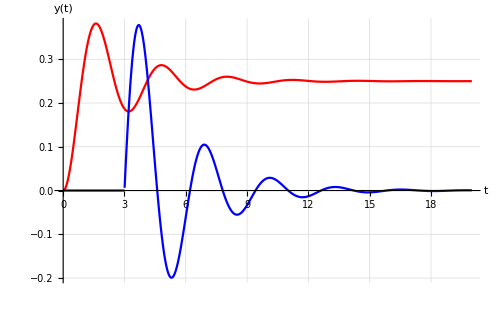

```mathematica
Plot[{rsys1,rsys2},{t,0,20},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

This method can be extended to multiple-input, multiple-output systems. You can also directly define transfer functions:

#### Calculate the poles of the transfer function

First in the general case

```mathematica
poles=Solve[ω0^2+2 ζ ω0 s+s^2==0,s]
```

{{s→-ζ ω0-√(-ω0^2+ζ^2 ω0^2)},{s→-ζ ω0+√(-ω0^2+ζ^2 ω0^2)}}

Now for the given sets of parameter values:

```mathematica
poles/.param//N//MatrixForm
```

((s→-0.4-1.95959 ⅈ) | (s→-0.4+1.95959 ⅈ)
(s→-1.41421-1.41421 ⅈ) | (s→-1.41421+1.41421 ⅈ)
(s→-7.4641) | (s→-0.535898))

State-Space Formalism

Beside transfer function models, also state-space models can be constructed.

### Second order system

We start here after writing down the first-order differential equations of our model. Writing this in matrix notation, should give us four equations that represent the system: the so-called A, B, C and D matrices.

```mathematica
aa4={{-b/m,-1/m},{k,0}};
```

```mathematica
MatrixForm[aa4]
```

(-b/m | -1/m
k | 0)

```mathematica
bb4={{1/m},{0}};
```

```mathematica
MatrixForm[bb4]
```

(1/m
0)

```mathematica
cc4={{1,0}};
```

```mathematica
MatrixForm[cc4]
```

(1 | 0)

```mathematica
dd4={{0}};
```

```mathematica
MatrixForm[dd4]
```

(0)

Let us set some values for the parameters in the system for calculation.

```mathematica
cond4={m->4,b->2,k->4}
```

{m→4,b→2,k→4}

The State=Space model can be constructed directly from the matrices:

```mathematica
ss4=StateSpaceModel[{aa4,bb4,cc4,dd4}]
```

-b/m-1/m1/mk00100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

You recognize the matrices you defined above.

```mathematica
CharacteristicPolynomial[aa4,s]
```

k/m+(b s)/m+s^2

From this State-Space system, a Transfer function model can be constructed. In this case it is not that complicated, since we only have one input, and one output. For a multiple input and multiple output system this wil generate a matrix of transfer functions, relating every input to every output.

In general case this gives:

```mathematica
tf4g=TransferFunctionModel[ss4,s]
```

s/(m (k/m+(b s)/m+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`m$CellContext`k1FalseFalseFalseAutomaticNoneAutomatic

The denominator of the Transfer Function can be recognized as the characteristic polynomial of the A-matrix.

Using the parameter values we defined above we obtain a form for further processing, like Bode Plots and input responses.

```mathematica
tf4=TransferFunctionModel[ss4/.cond4,s]
```

s/(4 (1+s/2+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
rsys4ga=OutputResponse[tf4,UnitStep[t],t];
```

```mathematica
rsys4gb=OutputResponse[tf4,DiracDelta[t],t];
```

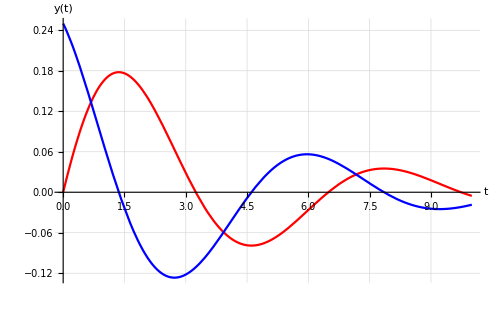

```mathematica
Plot[{rsys4ga,rsys4gb},{t,0,10},GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

### State-Space with initial conditions

```mathematica
aa5={{-0.5572,-0.7814},{0.7814,0}};
```

```mathematica
bb5={{1},{0}};
```

```mathematica
cc5={{1.9691,6.4493}};
```

```mathematica
dd5={{0}};
```

```mathematica
sys5=StateSpaceModel[{aa5,bb5,cc5,dd5}]
```

-0.5572-0.781410.7814001.96916.44930StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
x5i={1,0}
```

{1,0}

```mathematica
{x5a,x5b}=StateResponse[{sys5,x5i},0,{t,0,20}]
```

{InterpolatingFunction[{{0., 20.}}, <>][t],InterpolatingFunction[{{0., 20.}}, <>][t]}

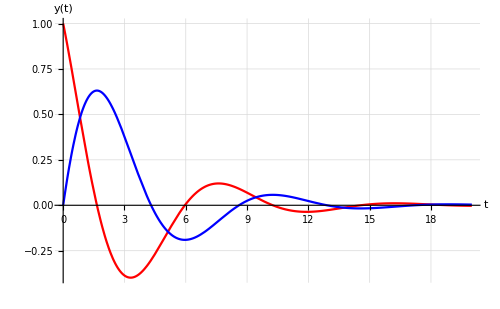

```mathematica
Plot[{x5a,x5b},{t,0,20},PlotRange->All,GridLines->Automatic,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

## From Differential equations

```mathematica
Clear[y,u,t];
eq=3 y''[t]+2 y'[t]+y[t]==u[t];
ss=StateSpaceModel[{eq},{{y'[t],0},{y[t],0}},{{u[t],0}},{y[t]},t];
ss=MinimalStateSpaceModel[ss]
```

-2/3-1/31/3100010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,Automatic,{{u[t],0}},Automatic,t

```mathematica
tf=Simplify[TransferFunctionModel[ss]]
```

1/(1+2 s+3 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11111FalseFalseFalseAutomaticNone,{u[s]}

#### Transferfunction ↔ State-Space Model

```mathematica
tf6=TransferFunctionModel[(1+s)/(s^2+4 s + 6),s]
```

(1+s)/(6+4 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11161FalseFalseFalseAutomaticNoneAutomatic

and construct the State-Space model from this transfer function:

```mathematica
StateSpaceModel[tf6]
```

010-6-41110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

TransferFunctionFactor is a useful function to find the poles.

```mathematica
TransferFunctionFactor[tf6]
```

(1+s)/((2-ⅈ √2+s) (2+ⅈ √2+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11121FalseFalseFalseAutomaticNoneAutomatic

From hereon, I would suggest, you use the help function, in combination with the “See also” section at the end of each help item, in order to explore the possibilities and get further inspiration.

Bode-Plots & Nyquist Plots

### Bode-Plots

First we generate the Bode Plots:

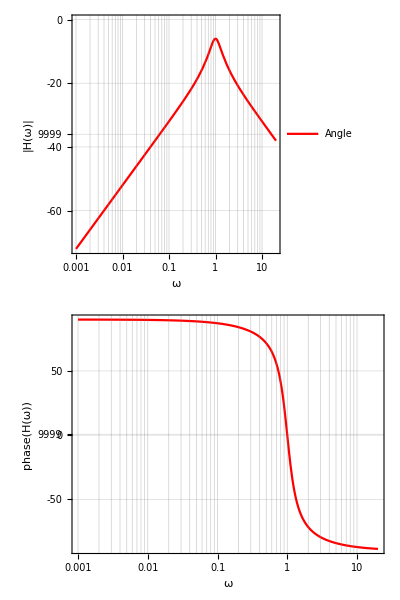

```mathematica
BodePlot[tf4,GridLines->Automatic,PlotStyle->Red,ImageSize->Large,FrameLabel->{{"ω","|H(ω)|"},{"ω","phase(H(ω))"}},PlotLegends->{"Angle"}]
```

#### Make a Bode-plot of the systems

With the function Manipulate you have the means to explore the effect of parameters in the system. Below you find an example of a second-order system where you can set the resonance frequency and the damping to explore the effect on the Bode diagram.

```mathematica
Manipulate[BodePlot[sys1/.{ζ->a,ω0->b},GridLines->Automatic,ImageSize->Medium],{{a,0.7},0,4},{{b,1},0,10}]
```

### Nyquist Plot

An alternative for the Bode-Plot is the so-called Nyquist plot. This represents the transfer function as a parametric plot in the complex plane, where ω is used as a parameter.

#### Nyquist plot of second order system

```mathematica
tf4
```

s/(4 (1+s/2+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

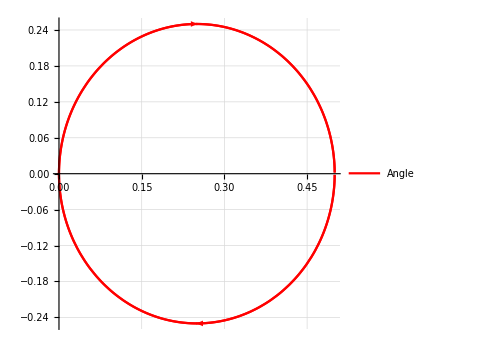

```mathematica
NyquistPlot[tf4,GridLines->Automatic,PlotStyle->Red,ImageSize->Medium,FrameLabel->{{"ω","|H(ω)|"},{"ω","phase(H(ω))"}},PlotLegends->{"Angle"}]
```

#### Nyquist Plot of previous system

```mathematica
{sys1,sys1/.param}
```

{1/(ω0^2+2 ζ ω0 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic,{1/(4+0.8 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11141FalseFalseFalseAutomaticNoneAutomatic,1/(4+2 √2 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11141FalseFalseFalseAutomaticNoneAutomatic,1/(4+8 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11141FalseFalseFalseAutomaticNoneAutomatic}}

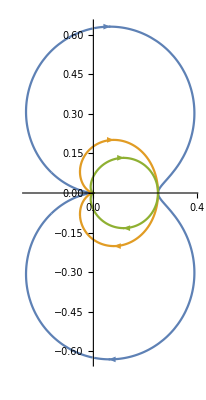

```mathematica
NyquistPlot[sys1/.param]
```

Output Response

Now we define a few responses to the three standard inputs: Unit-Step, Delta function and Sine function (here we suppress the output, since we are only interested in the graphical representation , however it might be illustrative to view at the mathematical expressions, this can even be calculated form the general form (no values used for the parameters)):

```mathematica
tf4step=OutputResponse[{tf4,{0,0}},UnitStep[t],t];
tf4pulse=OutputResponse[{tf4,{0,0}},DiracDelta[t],t];
tf4sin = OutputResponse[{tf4,{0,0}},Sin[2 π t],t];
```

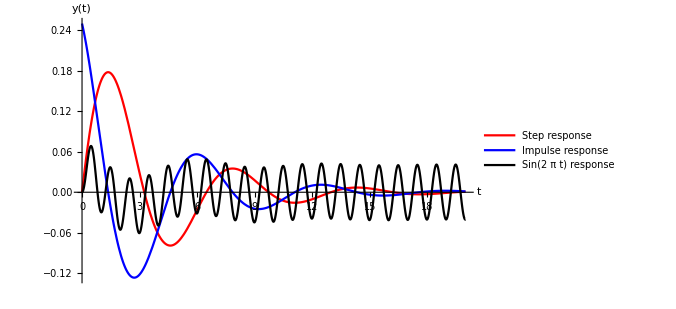

```mathematica
Plot[{tf4step,tf4pulse,tf4sin},{t,0,20},PlotRange->Full,PlotStyle->{Red,Blue,Black},AxesLabel->{"t","y(t)"},ImageSize->500,PlotLegends->{"Step response","Impulse response","Sin(2 π t) response"},BaseStyle->12]
```